```mathematica
Här kan man använda den inbyggda funktionen Fibonacci[n]
a)
```

```mathematica
Fibonacci[n]
```

```mathematica
Fibonacci[n]
```

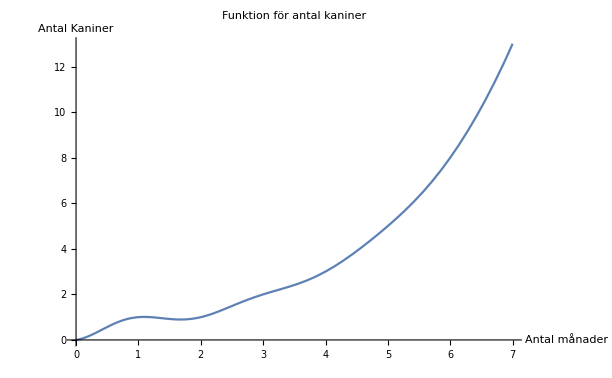

```mathematica
Plot[Fibonacci[n], {n, 0, 7}, PlotLabel->"Funktion för antal kaniner", AxesLabel->{"Antal månader", "Antal Kaniner"  }]
```

```mathematica
b)
```

```mathematica
Table[Fibonacci[n], {n, 1, 20}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

```mathematica
För varje  heltalsökning av n över talet 3  ((n + 1) /n   går kvoten närmare och närmare det så kallade gyllene snittet, vilket är ett irrationellt tal  runt 1.618.
Observera
```

```mathematica
n = 3
Fibonacci[n +1]/Fibonacci[n]
```

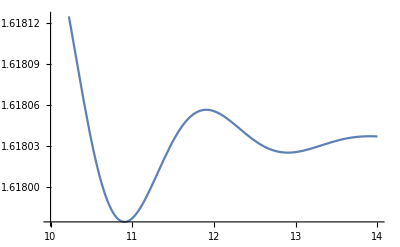

```mathematica
Plot[(Fibonacci[n + 1])/Fibonacci[n], {n, 10, 14}]
```

```mathematica
C) begränsningar:  För låga heltal är ökningen inte särskilt linjär och precis, utan ökningen skiftar upp och ned för de låga talen.
D) Istället för att använda den nämnda differensekvationen Subscript[p, n+2]=Subscript[p, n+1]+Subscript[p, n] kan man använda n multiplicerat med gyllene snittet n*φ
```